Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

February 22, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: Case Study: Eight SARS-CoV-2 Antivirals

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of February 17, 2011, we evaluated a dataset of 257 known drugs that contains the melting point, the logP, and the logS values for each of the compounds.

### Introduction/Background Information:

## Methodology

For this study, the list of 257 drugs was collected from the NCSSM Canvas website. The following analyses were conducted:

Drug data was imported into Mathematica

Data was summarized through descriptive statistics

The relationship between logP and logS was analyzed

The relationship between predicted logS and logS was analyzed

Data was filtered to find drugs with a logS above zero

### Data Import and Description:

```mathematica
drugData = Import["/Users/aakritilakshmanan/Downloads/drugGSEdata.csv"];
viableDrug=drugData;
drugData // TableForm;
```

## Results

### Descriptive Statistics

We determined the mean, median, standard deviation, and quartiles for our data set, and produced a box/whisker plot for each of the three variables. As can be seen in the box whisker plots below, most of the molecules examined have a melting point between 122 and 214 degrees. Melting point has the highest standard deviation out of the other variable examined, which means that there is more variance in the meting point values. In contrast, logP and logS are found within a much smaller range of values. In addition, the standard deviation is lower, which means that most of the compounds examined have similar logP and logS values. The logP dataset has a very close mean and median, which means that the logP data values are quite centered around the value of 2.

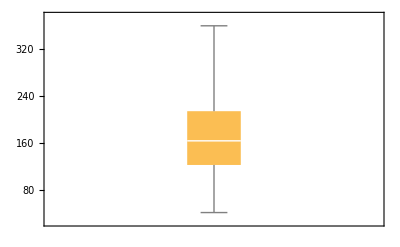
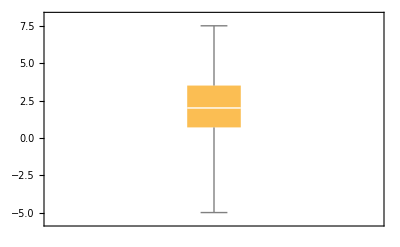
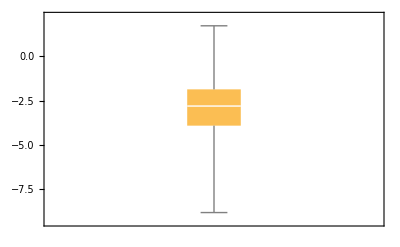
| MP | logP | logS
Mean | 168.28 | 2.08482 | -2.96464
Median | 163.5 | 2 | -2.812
Standard Deviation | 63.2095 | 1.96114 | 1.70755
Quartiles | {122.3,163.5,214.125} | {0.7,2,3.5} | {-3.9145,-2.812,-1.8735}
BoxWhisker Plot | -Graphics- | -Graphics- | -Graphics-

```mathematica
header = drugData[[1]];
drugData = Delete[drugData,1];
{name, mp, logP, logS} = Transpose[drugData];
descriptiveStats = Grid[{{"", header[[2]], header[[3]], header[[4]]}, {"Mean", Mean[mp], Mean[logP], Mean[logS]}, {"Median", Median[mp], Median[logP], Median[logS]}, {"Standard Deviation", StandardDeviation[mp], StandardDeviation[logP], StandardDeviation[logS]}, {"Quartiles", Quartiles[mp], Quartiles[logP], Quartiles[logS]}, {"BoxWhisker Plot", BoxWhiskerChart[v=mp], BoxWhiskerChart[logP], BoxWhiskerChart[logS]}}, Frame -> All]
```

### Plot of Results

#### Data Analysis of logP and logS

We prepared a plot of logP versus logS, as shown below. Based on this plot, we can see that there is a negative relationship between logP and logS. The line of best fit has a R squared of value of - .75, meaning that there is a quantifiable correlation between these two variables. However, this relationship is not extremely strong since the R squared value could be closer to one. Therefore it can be hypothesized that there remains another variable that also plays a role in logS in addition to logP. The line of best fit (shown in “normal” model) is:

```mathematica
logTogether = Transpose[{logP,logS}];
myFit = LinearModelFit[logTogether, x,x];  
Normal[myFit];
Print["logS =", TraditionalForm[Normal[myFit]]]
rval1=Correlation[logP,logS];
```

logS =-0.656499 x-1.59596

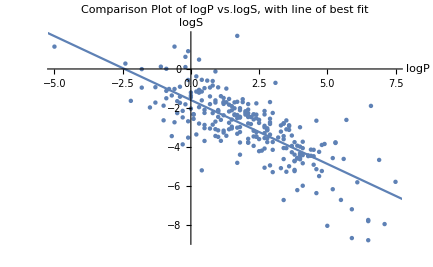

```mathematica
dataPlot = ListPlot[logTogether, AxesLabel->{"logP","logS"},PlotLabel->"Comparison Plot of logP vs.logS, with line of best fit",LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}];
fitPlot = Plot[myFit[x],{x,-100,100}];
Show[ dataPlot,fitPlot]
```

#### Data Analysis of logS and predicted logS

We prepared a plot of logS versus predicted logS, as shown below. Based on this plot, we can see that the empirical function for logS, known as the General Solubility Equation, is very correlated to the experimental logS values. The plotted line of best fit has an R squared value of  .81, which shows that there is a strong positive relationship between these two values. Compared to above, the R squared value has been increased by taking into account the melting point in addition to the logP value. Despite outliers that can be seen on this graph, overall, it can be concluded that the General Solubility Equation efficiently and accurately models the logS value of the selected compounds.

```mathematica
myFunction[x_,y_]= 0.8 - x- 0.01(y-25);
predictedLogS = List[];
For[i=1,i<(Length[logP]+1),i++,AppendTo[predictedLogS,myFunction[logP[[i]],mp[[i]]]]];
```

```mathematica
logSTogether = Transpose[{logS,predictedLogS}];
myLogSFit = LinearModelFit[logSTogether, x,x];  
Normal[myLogSFit];
Print["Predicted logS =", TraditionalForm[Normal[myLogSFit]]]
rval2=Correlation[logS,predictedLogS];
```

The line of best fit (shown in “normal” model) is:

Predicted logS =0.917945 x+0.00375459

```mathematica
datalogSPlot = ListPlot[logSTogether, AxesLabel->{"logS","Predicted logS"},PlotLabel->"Comparison Plot of logS vs. predicted logS, with line of best fit",LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}];
fitlogSPlot = Plot[myLogSFit[x],{x,-10,4}];
Show[ datalogSPlot,fitlogSPlot]
```

A graph of logS vs. predicted logS is shown below, with the line of best fit superimposed over the data:

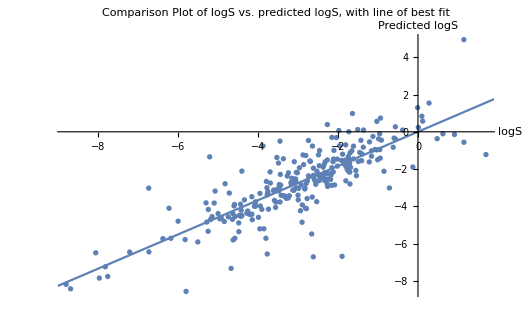

#### Determination of logS>0 drugs

We filtered the data to show which of the 257 drugs in our dataset have a logS value of greater than 0. Of the 257 drugs, we found 10 drugs with a logS value > 0. Drugs with a logS value over 0 are ranked 5 on the solubility ranking, and are too soluble for use as drugs within the body. As such, the following drugs can be filtered out and rejected before further analysis. These drugs are shown below:

```mathematica
Grid[
Map[
{
#[[1]],
#[[2]],
#[[3]],
#[[4]]
} &,
DeleteCases[viableDrug, a_ /; a[[4]] < 0]
],
Frame -> All]
```

Name | MP | logP | logS
Antipyrine | 112 | 0.3 | 0.48
Ascorbic acid | 191 | -2.4 | 0.277
Chloral hydrate | 57 | 1.7 | 1.7
Dimorpholamine | 41.5 | -0.2 | 0.098
Dyphylline | 158 | -1.1 | 0.118
Isoniazid | 171.4 | -0.9 | 0.009
Nicotinamide | 129.5 | -0.1 | 0.913
Proline | 221 | -0.6 | 1.149
Proxyphlline | 135.5 | -0.2 | 0.623
Sorbitol | 111 | -5 | 1.148

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on February 24, 2021.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References: